# Simulation of genomic data in multiparental populations

## Chaozhi Zheng Wageningen University and Research 1 Sep 2017

## Simulation by gene dropping

Population information

Population coding for common design

Inter-crossing via random mating

User pre-defined design pedigree

Simulate population-level pedigree

Simulate genomic data

Dropping FGL on the simulated pedigree

Replacing FGL by founder haplotypes

Simulated genotype missing and errors

## Load MagicGeneDropping

First set directory to the directory of the Mathematica packages.
Then load the package by functions Needs or Get. 
Use  the directory of the current notebook as the work directory.

```mathematica
SetDirectory[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"RABBIT_Packages"}]];
Get["MagicGeneDropping`"]
SetDirectory[NotebookDirectory[]]
```

D:\Chaozhi\StatisticalPackages\RABBIT Software\RABBIT_Tutorial

Get help information on functions or options by ?

```mathematica
?"MagicGeneDropping`*"
```

## Common experimental crosses

Coding for common experimental crosses

```mathematica
ls={"K generations of backcrss+S generations of selfing","K-way RIL by S generations of selfing","K-way RIL by S generations of sibling"};
TableForm[ls,TableHeadings->{{"bcK-selfS","Kwayril-selfS","Kwayril-sibS"},None}]
```

bcK-selfS | K generations of backcrss+S generations of selfing
Kwayril-selfS | K-way RIL by S generations of selfing
Kwayril-sibS | K-way RIL by S generations of sibling

```mathematica
names={"#backcross","#selfing"};
manbc=Manipulate[
code="bc"<>ToString[k]<>"-self"<>ToString[s];
pedigree=compilePopPedigree[code];
label=Style[code,Black,15,FontFamily->"Helvetica"];
pedigreePlot[pedigree,ImageSize->50 k+30,PlotLabel->label],{{k,1,names[[1]]},1,6,1},{{s,3,names[[2]]},0,10,1}];
names={"#founder","#selfing"};
kls=2^Range[1,5,1];
manrilself=Manipulate[
code=ToString[k]<>"wayril-self"<>ToString[s];
pedigree=compilePopPedigree[code];
label=Style[code,Black,15,FontFamily->"Helvetica"];
pedigreePlot[pedigree,ImageSize->50 k+30,PlotLabel->label],{{k,kls[[3]],names[[1]]},kls},{{s,3,names[[2]]},0,10,1}];
names={"#founder","#sibling"};
kls=2^Range[1,5,1];
manrilsib=Manipulate[
code=ToString[k]<>"wayril-sib"<>ToString[s];
pedigree=compilePopPedigree[code];
label=Style[code,Black,15,FontFamily->"Helvetica"];
pedigreePlot[pedigree,ImageSize->50 k+30,PlotLabel->label],{{k,kls[[3]],names[[1]]},kls},{{s,3,names[[2]]},1,10,1}];
manls={manbc,manrilself,manrilsib};
TabView[Thread[{"Backcross+selfing","RIL by selfing","RIL by sibling"}->manls],2,ImageSize->All]
```

123

## Experimental crosses by random mating

Here is an example of  multi-parental populations with inter-crossing via random mating.

```mathematica
popsize=20;
nFounder=10;
s=3;
mateScheme=Join[Table["RM1-NE-"<>ToString[popsize],{1}],Table["RM1-E",{3}],Table["Selfing",{s}]];
pedigree=simPedigree[nFounder,False,mateScheme];
Export["Example_Pedigree.csv",pedigree]
```

Example_Pedigree.csv

```mathematica
popsizels={10,20};
Manipulate[
mateScheme=Join[Table["RM1-NE-"<>ToString[popsize],{1}],Table["RM1-E",{3}],Table["Selfing",{s}]];
pedigree=simPedigree[nFounder,False,mateScheme];
pedigreePlot[pedigree,ImageSize->If[popsize==10,Large,Full],PlotLabel->mateScheme],{{popsize,popsizels[[1]],"Popsize"},popsizels},{{nFounder,4,"#founder"},2,10},{{s,3,"#selfing"},0,6,1}]
```

## Design pedigree

Here is an example of wheat design pedigree with 8 inbred founders (Mackay et al., 2014. G3: Genes|Genomes|Genetics 4: 1603–1610. )

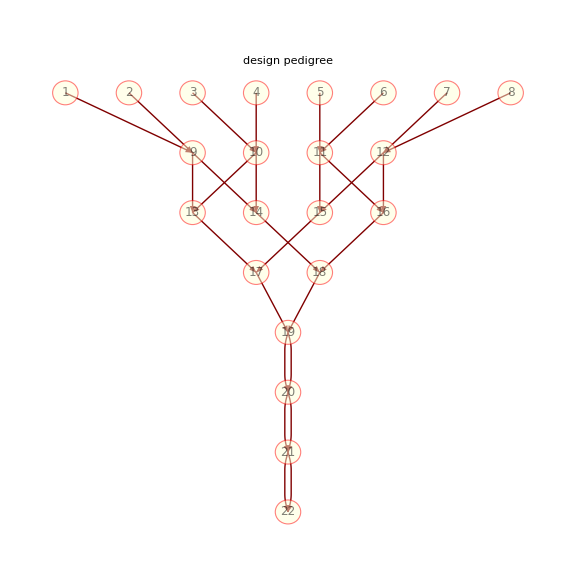

```mathematica
wheatped={{"Generation","Individual","Gender","Mother","Father"},{0,1,0,0,0},{0,2,0,0,0},{0,3,0,0,0},{0,4,0,0,0},{0,5,0,0,0},{0,6,0,0,0},{0,7,0,0,0},{0,8,0,0,0},{1,9,0,1,2},{1,10,0,3,4},{1,11,0,5,6},{1,12,0,7,8},{2,13,0,9,10},{2,14,0,9,10},{2,15,0,11,12},{2,16,0,11,12},{3,17,0,13,15},{3,18,0,14,16},{4,19,0,17,18},{5,20,0,19,19},{6,21,0,20,20},{7,22,0,21,21}};
wheatped=Join[wheatped[[All,;;3]],Transpose[{wheatped[[All,4;;5]]}],2];
pedigreePlot[wheatped,PlotLabel->Style["design pedigree",Black,20,Background->Yellow],ImageSize->Large]
```

## Simulate sample pedigree

```mathematica
?simPedigreeInfor
Options[simPedigreeInfor]
pedinforfile=simPedigreeInfor["4wayril-self3",sampleSize->20,outputFileID->"Example"]
```

simPedigreeInfor[pedigree] returns pedigreeInfor with sampleInfor being simulated from pedigree.

{sampleSize→100,sampleGender→Hermaphrodite,funnelFunction→(RandomSample[#1]&),outputFileID→}

Example_PedigreeInfor.csv

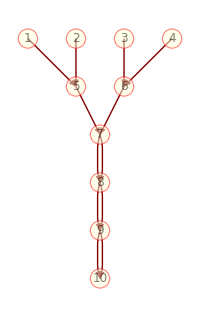

Pedigree-Information | The in-depth pedigree with funnelcode 1-2...4 |  |  | 
Generation | MemberID | Female=1/Male=2/Hermaphrodite=0 | MotherID | FatherID
0 | 1 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0
0 | 3 | 0 | 0 | 0
0 | 4 | 0 | 0 | 0
1 | 5 | 0 | 1 | 2
1 | 6 | 0 | 3 | 4
2 | 7 | 0 | 5 | 6
3 | 8 | 0 | 7 | 7
4 | 9 | 0 | 8 | 8
5 | 10 | 0 | 9 | 9
Pedigree-Information | The memberID and funnelcode for each sampled individual |  |  | 
ProgenyLine | MemberID | Funnelcode |  | 
ProgenyLine1 | 10 | 4-3-1-2 |  | 
ProgenyLine2 | 10 | 1-2-4-3 |  | 
ProgenyLine3 | 10 | 3-1-4-2 |  | 
ProgenyLine4 | 10 | 1-4-2-3 |  | 
ProgenyLine5 | 10 | 2-1-3-4 |  | 
ProgenyLine6 | 10 | 4-2-3-1 |  | 
ProgenyLine7 | 10 | 4-2-3-1 |  | 
ProgenyLine8 | 10 | 2-4-1-3 |  | 
ProgenyLine9 | 10 | 2-1-4-3 |  | 
ProgenyLine10 | 10 | 4-2-3-1 |  | 
ProgenyLine11 | 10 | 4-3-1-2 |  | 
ProgenyLine12 | 10 | 1-2-3-4 |  | 
ProgenyLine13 | 10 | 2-4-1-3 |  | 
ProgenyLine14 | 10 | 4-3-1-2 |  | 
ProgenyLine15 | 10 | 4-3-1-2 |  | 
ProgenyLine16 | 10 | 4-3-1-2 |  | 
ProgenyLine17 | 10 | 1-3-2-4 |  | 
ProgenyLine18 | 10 | 3-4-2-1 |  | 
ProgenyLine19 | 10 | 3-1-2-4 |  | 
ProgenyLine20 | 10 | 4-2-3-1 |  |

```mathematica
pedigreeInfor=Import[pedinforfile];
pedigreePlot[splitPedigreeInfor[pedigreeInfor][[2]],ImageSize->200]
TextGrid[pedigreeInfor,Frame->All]
```

## Simulation genomic data

```mathematica
?magicGeneDropping
Options[magicGeneDropping]
```

magicGeneDropping [founderhaplo, popdesign] simulates genomic data in the population with the breeding design specified by popdesign. The founderhaplo specifies the founder haplotypes and genetic map over a set of markers or the input filename. The popdesign speficies the breeding design information in several possible ways: a list of mating schemes from founder population to the last generation, a list of values denoting the junction distribution, or a filename for population pedigree information.

{founderAllelicError→0.005,offspringAllelicError→0.005,isFounderInbred→True,dropMonomorphic→False,interferenceStrength→0,isObligate→False,phredQualScore→30,founderGenotypeMissing→0,founderReadDepth→0,offspringGenotypeMissing→0,offspringReadDepth→0,depthDistribution→NegativeBinomial-1,outputFileID→,isPrintTimeElapsed→True}

```mathematica
depth=RandomChoice[{0,2}]; (*depth=0 means SNP-array data*)
datafiles=magicGeneDropping["Arabidopsis_MAGIC_19FounderHaplo.csv",pedinforfile,outputFileID->"Example",founderGenotypeMissing->0.1,founderReadDepth->depth,offspringGenotypeMissing->0.1,offspringReadDepth->depth];
```

magicGeneDropping. Start date = Thu 25 Apr 2019 09:51:51

Time elapsed = 0. Seconds. 	Start simulating offspring genomes in terms of FGL lists.

Time elapsed = 0.7 Seconds. 	Start dropping founder alleles on the offspring FGL lists.

Time elapsed = 0.9 Seconds. 	Start simulating allelic errors in founders and offspring.

The realized fraction of missing genotypes in founders: 0.324

The realized fraction of missing genotypes in offspring: 0.325

Saving true values and simulated data. Thu 25 Apr 2019 09:51:54
	True FGL | Example_TrueValues_Fgl.txt
True FGL diplotype | Example_TrueValues_FglDiplotype.csv
True diplotype | Example_TrueValues_Diplotype.csv
Observed genotype | Example_ObservedGenotype.csv

Done! Finished date =Thu 25 Apr 2019 09:51:54. 	Time elapsed = 3.2 Seconds.

## View output files

```mathematica
TabView[
Thread[{"True FGL","True FGL diplotype","True diplotype","Observed genotype"}->
Table[
data=If[i==1,ReadList[datafiles[[i]]],Import[datafiles[[i]],Path->Directory[]]];
Column[{datafiles[[i]]<>"\n(only several marks/individuals are shown)",TableForm[Take[#,UpTo[6]]&/@Take[data,UpTo[Switch[i,1,2,_,15]]]]},Frame->All],{i,1,Length[datafiles]}]],4,ImageSize->Automatic]
```

1234